```mathematica
(*THIS IS THE CHANGE 
William Rodrigues
10/9/17
Hermite interpolation*)
```

```mathematica
(*NUMBER TWO IS HANDED IN ON PAPER*)
(*2. Complete the veriﬁcation that the functions uihi and vihi satisfy the requirements for a Hermite interpolation.*)

(*
count=0;
If[Exponent[ui[x],x]==1,
count++,
Print["Degree of ui != 1"]
];
If[ui[xi]==1,
count++,
Print["ui[xi]!=1"]
];
If[D[ui[xi],x]==D[-hi[xi],x],
count++,
Print["ui'(xi) != -hi'(xi)"]
];
If[Exponent[vi[x],x]==1,
count++,
Print["Degree of vi != 1"]
];
If[vi[xi]==0,
count++,
Print["vi[xi]!=0"]
];
If[D[vi[xi],x]==1,
count++,
Print["vi'(xi) != 1"]
];
If[count==6,
Print["uihi and vihi satisfy the requirements for a Hermite interpolation"],
Print["You have problems"]
];
*)
```

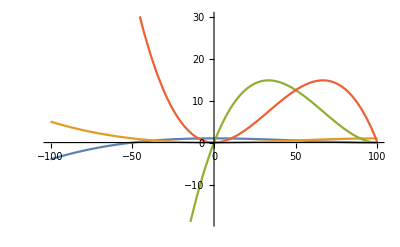

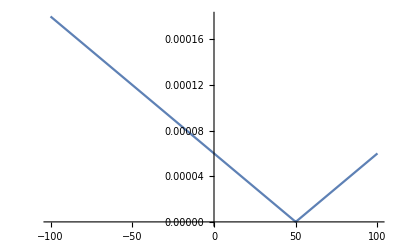

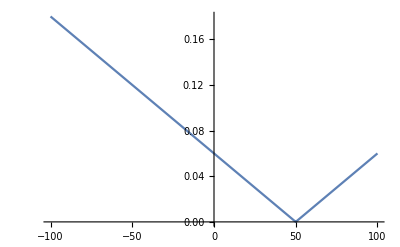

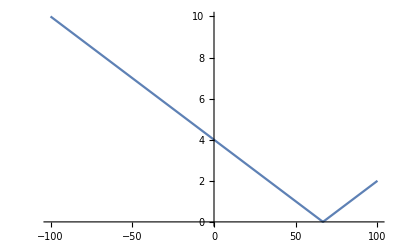

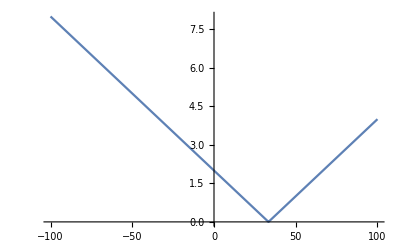

```mathematica
(*5. Plot the 4 Hermite cubics and verify by inspection that they satisfy the requirements of Deﬁnition 3.5.1.*)

b=100;
a=0;

h0[x_]=3(((b-x)/(b-a))^2)-2(((b-x)/(b-a))^3);
h1[x_]:=3(((x-a)/(b-a))^2)-2(((x-a)/(b-a))^3);
s0[x_]:=(((b-x)^2)/(b-a))-(((b-x)^3)/((b-a))^2);
s1[x_]:=(((x-a)^2)/(b-a))-(((x-a)^3)/((b-a))^2);

Plot[{h0[x],h1[x],s0[x],s1[x]},{x,-100,100}]


rightdh0[h0_,h_,x_]:=(h0[x+h]-h0[x])/h;
leftdh0[h0_,h_,x_]:=(h0[x]-h0[x-h])/h;
Plot[Abs[leftdh0[h0,0.1,x]-rightdh0[h0,0.1,x]],{x,-100,100}]

rightdh1[h1_,h_,x_]:=(h1[x+h]-h1[x])/h;
leftdh1[h1_,h_,x_]:=(h1[x]-h1[x-h])/h;
Plot[Abs[leftdh1[h1,100,x]-rightdh1[h1,100,x]],{x,-100,100}]

rightds0[s0_,h_,x_]:=(s0[x+h]-s0[x])/h;
leftds0[s0_,h_,x_]:=(s0[x]-s0[x-h])/h;
Plot[Abs[leftds0[s0,100,x]-rightds0[s0,100,x]],{x,-100,100}]

rightds1[s1_,h_,x_]:=(s1[x+h]-s1[x])/h;
leftds1[s1_,h_,x_]:=(s1[x]-s1[x-h])/h;
Plot[Abs[leftds1[s1,100,x]-rightds1[s1,100,x]],{x,-100,100}]

(*Tried showing a derivative exist on the entire interval but was having a problem with that*)
```

```mathematica
1
```

1